```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin hourly price: Recent (≥ 2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2026 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-04-21

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2018-05-15

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2026-04-22,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

69531

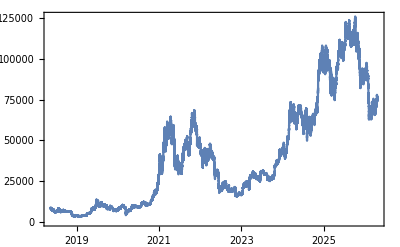

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Bitcoin_price-hourly-20180515-20260421.csv

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

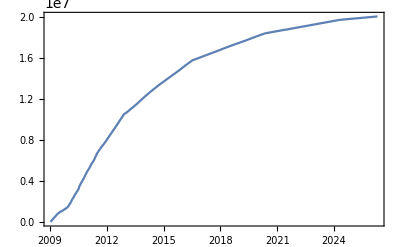

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1776339942}

```mathematica
{hourlyPrices[[1]][[1]],hourlyPrices[[-1]][[1]]}
```

{1526364000,1776816000}

```mathematica
{supplyFunction[hourlyPrices[[1]][[1]]], supplyFunction[hourlyPrices[[-3]][[1]]]}
```

{1.70343×10^7,2.00192×10^7}

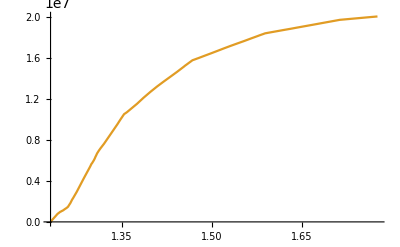

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPrices
```

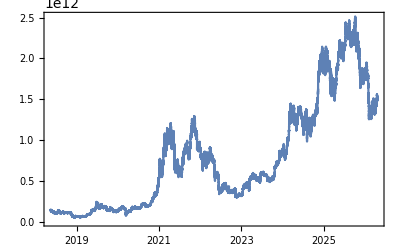

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-11-23", lastPriceDate}, {"2026-02-06", lastPriceDate}}
```

{{2025-11-23,2026-04-21},{2026-02-06,2026-04-21}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1763848800,1776722400},{1770328800,1776722400}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{149,74}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1763848800,28.1594},{1770328800,27.8738}}

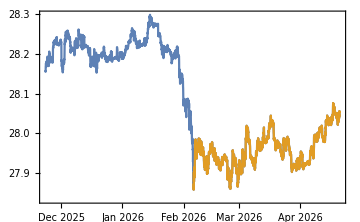

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{2.81575,0.436571},{1.04717,0.881905}}

```mathematica
Length/@bubblesScaled
```

{3557,1757}

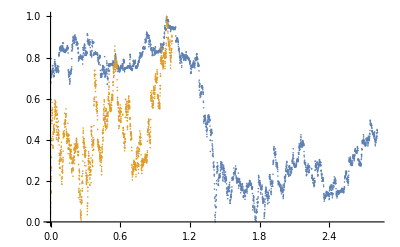

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Bitcoin-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Bitcoin-1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Bitcoin-2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.08
```

0.08

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{19.8501,3530.9},{19.918,1730.82}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{6.82337,0.0439672,0.00311459},{7.6753,0.0666147,0.00670111}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

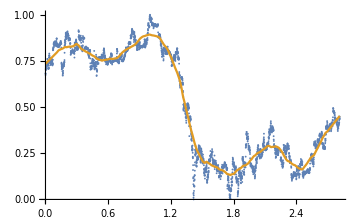
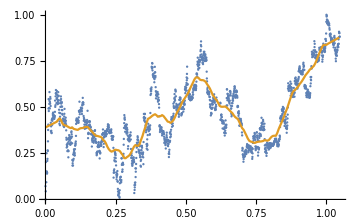

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

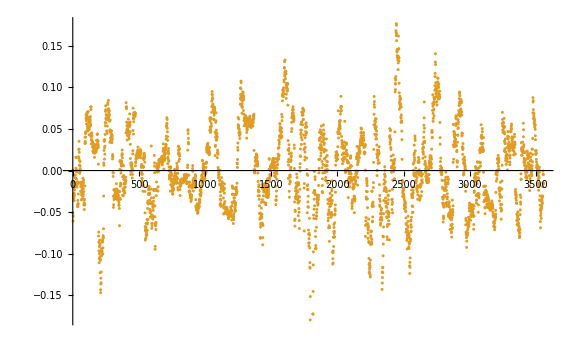
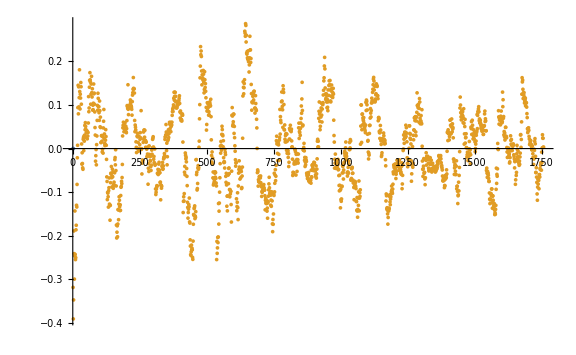

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0508091,0.0886665}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{9.18005,13.8052}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{9.18005 > 6.82337,13.8052 > 7.6753}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0509443,0.089148}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0509443 > 0.0439672,0.089148 > 0.0666147}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.043921,0.0664718}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0509894,0.0893091}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0509894 > 0.0439672,0.0893091 > 0.0666147}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0439599,0.0665919}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Select last bubble for fitting: *)
bubble=bubbleN
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{19.918,1730.82}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.04717

2.85798

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0405405

```mathematica
(* Define 3 days resolution scaled initial time step *)
stepTi=3/bubblesDays[[bubble]]//N
```

0.0405405

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Wed 22 Apr 2026 08:27:40GMT+2[]

{3775.39,{{a→2.45382,b→-2.17828,c→0.0162069,d→-0.123359,T_1→0.,tc→1.08781,m→0.1,ω→3.5,RSS→32.19,ℛerror→0.0183943,ℛσ→0.135394,LL→4007.63,ρ→0.982663,σ→-0.0250947,μ→-8.17774×10^-18},{a→3.088,b→-2.55515,c→-0.162293,d→0.0485457,T_1→0.0405405,tc→1.777,m→0.1,ω→14.,RSS→21.0665,ℛerror→0.0125321,ℛσ→0.111748,LL→3936.43,ρ→0.97631,σ→-0.0241724,μ→-3.31147×10^-17},{a→3.51624,b→-2.96925,c→-0.150896,d→-0.0398875,T_1→0.0810811,tc→1.81754,m→0.1,ω→13.9,RSS→21.8135,ℛerror→0.0135319,ℛσ→0.116111,LL→3790.84,ρ→0.979118,σ→-0.0235973,μ→-4.74847×10^-17},{a→1.22093,b→-0.855859,c→-0.00116224,d→0.138068,T_1→0.121622,tc→1.08781,m→0.2,ω→7.,RSS→26.9444,ℛerror→0.0174623,ℛσ→0.131889,LL→3636.24,ρ→0.984073,σ→-0.0234377,μ→1.21611×10^-18},{a→2.9964,b→-2.81348,c→-0.0493424,d→-0.186469,T_1→0.162162,tc→1.08781,m→0.1,ω→3.6,RSS→19.7108,ℛerror→0.0133724,ℛσ→0.115404,LL→3472.78,ρ→0.979021,σ→-0.0235069,μ→-1.72242×10^-17},{a→3.87302,b→-3.62493,c→0.00527732,d→-0.196323,T_1→0.202703,tc→1.24997,m→0.1,ω→5.6,RSS→17.1151,ℛerror→0.0121729,ℛσ→0.110096,LL→3308.94,ρ→0.976641,σ→-0.023649,μ→-1.30772×10^-17},{a→5.50836,b→-5.05156,c→0.010686,d→0.199252,T_1→0.243243,tc→1.65538,m→0.1,ω→11.1,RSS→13.2079,ℛerror→0.00987876,ℛσ→0.0991697,LL→3157.35,ρ→0.972473,σ→-0.0230993,μ→7.58332×10^-18},{a→4.70437,b→-4.38303,c→0.151199,d→-0.138246,T_1→0.283784,tc→1.41213,m→0.1,ω→7.8,RSS→12.9072,ℛerror→0.0101791,ℛσ→0.100654,LL→3009.32,ρ→0.973161,σ→-0.0231539,μ→5.776×10^-17},{a→6.05185,b→-5.52892,c→-0.197752,d→0.0300722,T_1→0.324324,tc→1.777,m→0.1,ω→12.7,RSS→11.3969,ℛerror→0.00950535,ℛσ→0.0972524,LL→2877.68,ρ→0.973432,σ→-0.0222591,μ→8.20972×10^-17},{a→5.86937,b→-5.36821,c→-0.157678,d→0.122321,T_1→0.364865,tc→1.73646,m→0.1,ω→12.1,RSS→11.0858,ℛerror→0.00980177,ℛσ→0.0987423,LL→2759.93,ρ→0.976197,σ→-0.0214062,μ→-8.60733×10^-17},{a→1.31386,b→-0.763607,c→-0.205798,d→-0.0558841,T_1→0.405405,tc→1.81754,m→1.,ω→13.7,RSS→6.64012,ℛerror→0.00625246,ℛσ→0.0788501,LL→2627.14,ρ→0.964322,σ→-0.0208645,μ→-9.65264×10^-18},{a→1.26107,b→-0.712715,c→-0.20115,d→-0.0703354,T_1→0.445946,tc→1.81754,m→1.,ω→14.,RSS→6.0535,ℛerror→0.00609618,ℛσ→0.0778432,LL→2451.21,ρ→0.962362,σ→-0.0211449,μ→9.8658×10^-18},{a→1.23678,b→-0.68676,c→-0.200215,d→-0.0746425,T_1→0.486486,tc→1.81754,m→1.,ω→13.9,RSS→5.84817,ℛerror→0.00632919,ℛσ→0.0792991,LL→2306.73,ρ→0.965829,σ→-0.0205416,μ→-6.84577×10^-19},{a→1.13511,b→-0.551237,c→-0.122206,d→-0.178143,T_1→0.527027,tc→1.85808,m→1.,ω→13.7,RSS→5.32937,ℛerror→0.0062259,ℛσ→0.0786293,LL→2141.96,ρ→0.965539,σ→-0.020452,μ→-2.45647×10^-17}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

62.9231

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.08781 | ℛσ→0.135394 | LL→4007.63
T_1→0.0405405 | tc→1.777 | ℛσ→0.111748 | LL→3936.43
T_1→0.0810811 | tc→1.81754 | ℛσ→0.116111 | LL→3790.84
T_1→0.121622 | tc→1.08781 | ℛσ→0.131889 | LL→3636.24
T_1→0.162162 | tc→1.08781 | ℛσ→0.115404 | LL→3472.78
T_1→0.202703 | tc→1.24997 | ℛσ→0.110096 | LL→3308.94
T_1→0.243243 | tc→1.65538 | ℛσ→0.0991697 | LL→3157.35
T_1→0.283784 | tc→1.41213 | ℛσ→0.100654 | LL→3009.32
T_1→0.324324 | tc→1.777 | ℛσ→0.0972524 | LL→2877.68
T_1→0.364865 | tc→1.73646 | ℛσ→0.0987423 | LL→2759.93
T_1→0.405405 | tc→1.81754 | ℛσ→0.0788501 | LL→2627.14
T_1→0.445946 | tc→1.81754 | ℛσ→0.0778432 | LL→2451.21
T_1→0.486486 | tc→1.81754 | ℛσ→0.0792991 | LL→2306.73
T_1→0.527027 | tc→1.85808 | ℛσ→0.0786293 | LL→2141.96

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.5714

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.08781

1.85808

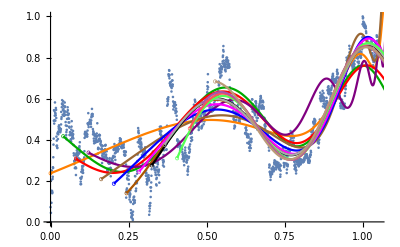

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0405405,0.0810811,0.121622,0.162162,0.202703,0.243243,0.283784,0.324324,0.364865,0.405405,0.445946,0.486486,0.527027}

{0.0183943,0.0125321,0.0135319,0.0174623,0.0133724,0.0121729,0.00987876,0.0101791,0.00950535,0.00980177,0.00625246,0.00609618,0.00632919,0.0062259}

{32.19,21.0665,21.8135,26.9444,19.7108,17.1151,13.2079,12.9072,11.3969,11.0858,6.64012,6.0535,5.84817,5.32937}

{0.135394,0.111748,0.116111,0.131889,0.115404,0.110096,0.0991697,0.100654,0.0972524,0.0987423,0.0788501,0.0778432,0.0792991,0.0786293}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

1757

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

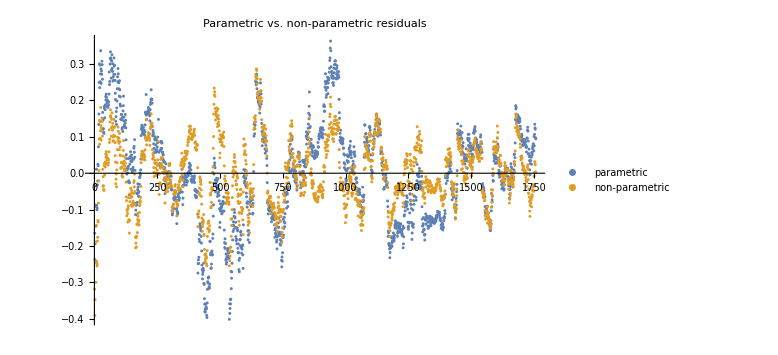

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{13.8052,32.19}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0893091,0.135625}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.00797611,0.0183943}

```mathematica
selN=Length[T1s];
selN
```

14

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{1757,1686,1615,1544,1473,1401,1330,1259,1188,1116,1045,974,903,832}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{1757,1686,1615,1544,1473,1401,1330,1259,1188,1116,1045,974,903,832}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-Bitcoin-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{1757,1686,1615,1544,1473,1401,1330,1259,1188,1116,1045,974,903,832}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.0183943,0.0125321,0.0135319,0.0174623,0.0133724,0.0121729,0.00987876,0.0101791,0.00950535,0.00980177,0.00625246,0.00609618,0.00632919,0.0062259}

```mathematica
RSSs
```

{32.19,21.0665,21.8135,26.9444,19.7108,17.1151,13.2079,12.9072,11.3969,11.0858,6.64012,6.0535,5.84817,5.32937}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0886665,0.085695,0.0859018,0.0853576,0.0862244,0.0876833,0.0877803,0.0819097,0.0808572,0.0801779,0.0725754,0.0701827,0.0716106,0.0726241}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.957115,σ→-0.0256802,μ→3.39561×10^-6},{ρ→0.961475,σ→-0.02355,μ→-4.74022×10^-6},{ρ→0.962838,σ→-0.0231931,μ→-0.0000341686},{ρ→0.962211,σ→-0.0232357,μ→0.000020072},{ρ→0.963777,σ→-0.022989,μ→-0.0000401984},{ρ→0.96435,σ→-0.0231955,μ→0.0000156706},{ρ→0.964144,σ→-0.0232864,μ→-0.0000777752},{ρ→0.960479,σ→-0.0227908,μ→-0.000022105},{ρ→0.961491,σ→-0.022213,μ→0.0000329448},{ρ→0.960578,σ→-0.0222804,μ→0.000119666},{ρ→0.957236,σ→-0.0209865,μ→-0.000103676},{ρ→0.955965,σ→-0.0205866,μ→0.0000729145},{ρ→0.958185,σ→-0.0204799,μ→0.000026076},{ρ→0.960011,σ→-0.0203198,μ→0.0000933576}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[3.39561×10^-6,{0.957115},0.000659473],ARProcess[-4.74022×10^-6,{0.961475},0.000554604],ARProcess[-0.0000341686,{0.962838},0.00053792],ARProcess[0.000020072,{0.962211},0.000539898],ARProcess[-0.0000401984,{0.963777},0.000528493],ARProcess[0.0000156706,{0.96435},0.000538032],ARProcess[-0.0000777752,{0.964144},0.000542257],ARProcess[-0.000022105,{0.960479},0.000519421],ARProcess[0.0000329448,{0.961491},0.000493418],ARProcess[0.000119666,{0.960578},0.000496415],ARProcess[-0.000103676,{0.957236},0.000440435],ARProcess[0.0000729145,{0.955965},0.00042381],ARProcess[0.000026076,{0.958185},0.000419427],ARProcess[0.0000933576,{0.960011},0.000412893]}

{4010.29,3938.26,3788.68,3625.19,3465.89,3285.41,3124.69,2974.71,2836.02,2726.27,2560.42,2401.26,2242.61,2065.26}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

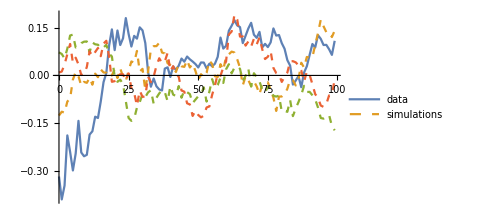
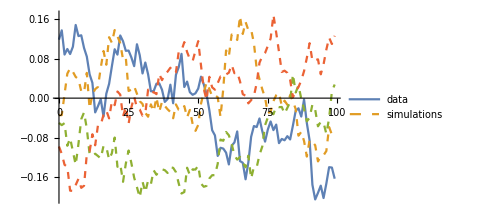
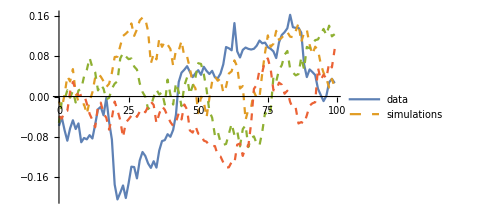
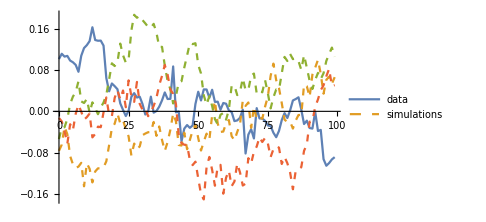
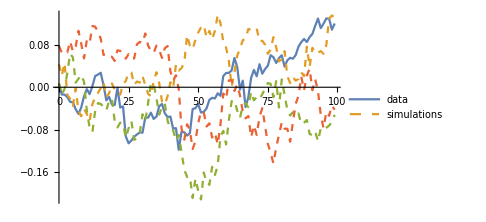
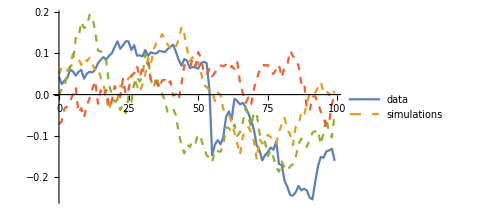
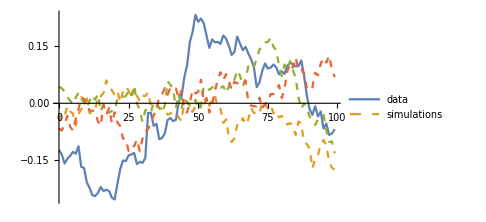
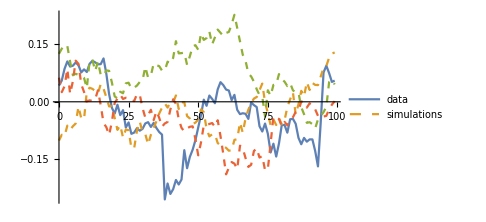

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{19.918,1730.82},{19.7156,1660.09},{19.8613,1588.9},{20.0198,1517.69},{20.165,1446.5},{19.8933,1374.86},{19.9488,1303.79},{20.0305,1232.68},{20.111,1161.58},{19.8202,1089.96},{20.0816,1018.62},{20.2425,947.407},{19.9533,876.786},{20.1739,805.5}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

1730.82

19.918

{1730.82,1660.09,1588.9,1517.69,1446.5,1374.86,1303.79,1232.68,1161.58,1089.96,1018.62,947.407,876.786,805.5}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 2.00975 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 2.00984 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 288729 Kb

Memory Used: 1.7346 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,2,0,1,10,113,21,37,23,205,155,172,248}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.002,0.,0.001,0.01,0.113,0.021,0.037,0.023,0.205,0.155,0.172,0.248}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,False,True,True,True,False,False,False,False}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

7

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

9

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.08781

1

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

7

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→5.50836,b→-5.05156,c→0.010686,d→0.199252,T_1→0.243243,tc→1.65538,m→0.1,ω→11.1,RSS→13.2079,ℛerror→0.00987876,ℛσ→0.0991697,LL→3157.35,ρ→0.972473,σ→-0.0230993,μ→7.58332×10^-18,index→7}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

7

{a→5.50836,b→-5.05156,c→0.010686,d→0.199252,T_1→0.243243,tc→1.65538,m→0.1,ω→11.1,RSS→13.2079,ℛerror→0.00987876,ℛσ→0.0991697,LL→3157.35,ρ→0.972473,σ→-0.0230993,μ→7.58332×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.1

11.1

1.65538

3157.35

```mathematica
t1=Subscript[T, 1]/.fit
```

0.243243

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

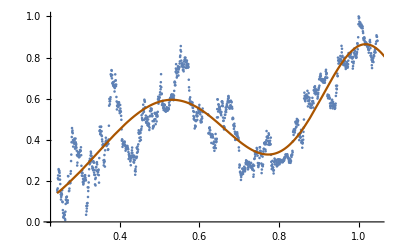

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→5.50836,b→-5.05156,c→0.010686,d→0.199252,T_1→0.243243,tc→1.65538,m→0.1,ω→11.1,RSS→13.2079,ℛerror→0.00987876,ℛσ→0.0991697,LL→3157.35,ρ→0.972473,σ→-0.0230993,μ→7.58332×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.972473,σ→-0.0230993,μ→7.58332×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92002

{1.63265,1.65538}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92003

{1.63265,1.65538,1.67882}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.04717

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Mon 1 Jun 2026 08:58:00

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Tue 2 Jun 2026 23:31:15

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Thu 4 Jun 2026 15:16:37

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Thu 28 May 2026 01:05:46

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Wed 17 Jun 2026 07:18:17

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Thu 23 Apr 2026 20:55:34

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Fri 6 Feb 2026 00:00:00 | tc→1.08781 | Thu 23 Apr 2026 20:55:34
T_1→0.0405405 | Sun 8 Feb 2026 20:45:24 | tc→1.777 | Thu 11 Jun 2026 13:47:28
T_1→0.0810811 | Wed 11 Feb 2026 17:30:48 | tc→1.81754 | Sun 14 Jun 2026 10:32:52
T_1→0.121622 | Sat 14 Feb 2026 14:16:12 | tc→1.08781 | Thu 23 Apr 2026 20:55:34
T_1→0.162162 | Tue 17 Feb 2026 11:01:37 | tc→1.08781 | Thu 23 Apr 2026 20:55:34
T_1→0.202703 | Fri 20 Feb 2026 07:47:01 | tc→1.24997 | Tue 5 May 2026 07:57:12
T_1→0.243243 | Mon 23 Feb 2026 04:32:25 | tc→1.65538 | Tue 2 Jun 2026 23:31:15
T_1→0.283784 | Thu 26 Feb 2026 01:17:50 | tc→1.41213 | Sat 16 May 2026 18:58:49
T_1→0.324324 | Sat 28 Feb 2026 22:03:14 | tc→1.777 | Thu 11 Jun 2026 13:47:28
T_1→0.364865 | Tue 3 Mar 2026 18:48:38 | tc→1.73646 | Mon 8 Jun 2026 17:02:04
T_1→0.405405 | Fri 6 Mar 2026 15:34:03 | tc→1.81754 | Sun 14 Jun 2026 10:32:52
T_1→0.445946 | Mon 9 Mar 2026 12:19:27 | tc→1.81754 | Sun 14 Jun 2026 10:32:52
T_1→0.486486 | Thu 12 Mar 2026 09:04:51 | tc→1.81754 | Sun 14 Jun 2026 10:32:52
T_1→0.527027 | Sun 15 Mar 2026 05:50:16 | tc→1.85808 | Wed 17 Jun 2026 07:18:17

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

3.41811

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

2.17053

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
Exp[lastScaledM]
```

0.881905

2.4155

```mathematica
lastPriceDate
```

2026-04-21

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1776722400&timeEnd=1776808800&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

```mathematica
latestMarketCapInner=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]]
```

```mathematica
(* Build a list of timeCloses and marketCaps: *)
latestMarketCapWithTime=SortBy[MapThread[{#1, #2[[2]][[7]]}&,{latestMarketCapInner[[2;;-1;;5]], latestMarketCapInner[[5;;-1;;5]]}], First][[-1]]
```

{timeClose→2026-04-21T23:59:59.999Z,marketCap→1.52853954167766×10^12}

```mathematica
latestMarketCap=latestMarketCapWithTime[[2]][[2]]/10^7
```

152853.954167766

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,1}]
```

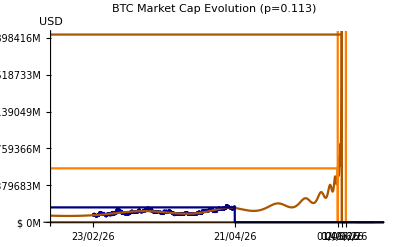

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_MarketCapPrediction-2026-04-21.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

554523.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

1.9308×10^6

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
tcToDate[lastScaledTc]
```

Tue 21 Apr 2026 00:00:00

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

76355.5

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]//N
```

276423.

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

962342.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i/1000]]<>"K"},{i,min, max,Max[1,IntegerPart[max/100000]]10000}]
ticksVPrice[1, 100000]
```

{{1,$0K},{10001,$10K},{20001,$20K},{30001,$30K},{40001,$40K},{50001,$50K},{60001,$60K},{70001,$70K},{80001,$80K},{90001,$90K}}

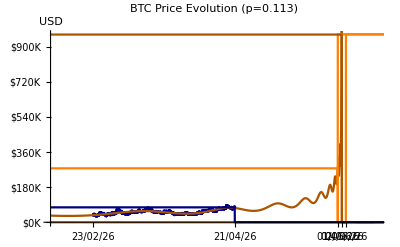

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2026-04-21.png